[1/2] 正在点燃并发暴胀宇宙...

[2/2] 演化停止，启动全息肖尔形态学分析...

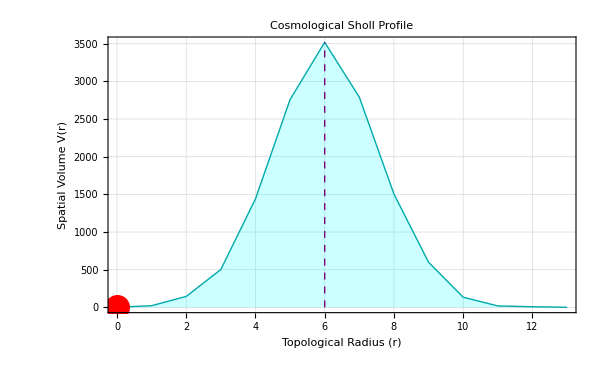

Sholl Metric (Neuro-Morphology) | Cosmological Physical Mapping | Extracted Value
Primary Branches | Big Bang Initial Degrees of Freedom | 25
Sholl Critical Radius (r_c) | Turnaround Time (Expansion to Collapse) | 6
Sholl Critical Value (N_max) | Maximum Equator Spatial Volume | 3519
Ramification Index | Inflation Amplification Factor | 140.76
Sholl Regression Coeff (k) | Big Crunch Topological Deceleration | -1.3474 (R^2=0.98)

```mathematica
ClearAll["Global`*"];
SeedRandom[];

(* ==========================================================*)
(*1. 并发暴胀引擎 (完全原生 Union 去重，无人工排序干预)*)
(* ==========================================================*)
StepEvolution[g_Graph,window_]:=Module[{allEdges,activeEdges,nActive,usedEdges,updates,tempE1,tempE2,x,y,z,wCounter,newVertices,newActive,newFrozen,remainingEdges},allEdges=EdgeList[g];
activeEdges=RandomSample[Cases[allEdges,_UndirectedEdge]];
nActive=Length[activeEdges];
If[nActive<2,Return[{g,0}]];
usedEdges={};updates={};
Do[tempE1=activeEdges[[i]];
If[!MemberQ[usedEdges,tempE1],Do[tempE2=activeEdges[[j]];
If[!MemberQ[usedEdges,tempE2]&&Length[Intersection[List@@tempE1,List@@tempE2]]==1,AppendTo[updates,{tempE1,tempE2}];
AppendTo[usedEdges,tempE1];AppendTo[usedEdges,tempE2];
Break[];],{j,i+1,Min[i+window,nActive]}]],{i,1,nActive}];
If[Length[updates]==0,Return[{g,0}]];
wCounter=Max[VertexList[g]];
newVertices={};newActive={};newFrozen={};
Do[y=Intersection[List@@pair[[1]],List@@pair[[2]]][[1]];
x=Complement[List@@pair[[1]],{y}][[1]];
z=Complement[List@@pair[[2]],{y}][[1]];
wCounter++;
AppendTo[newVertices,wCounter];
newActive=Join[newActive,{UndirectedEdge[x,z],UndirectedEdge[x,wCounter],UndirectedEdge[wCounter,z]}];
newFrozen=Join[newFrozen,{DirectedEdge[x,y],DirectedEdge[y,z]}];,{pair,updates}];
remainingEdges=Complement[allEdges,Flatten[updates]];
{Graph[Union[Join[VertexList[g],newVertices]],Union[Join[remainingEdges,newActive,newFrozen]]],Length[updates]}];

(* ==========================================================*)
(*2. 并发宇宙演化采集 (40 步)*)
(* ==========================================================*)
Print[Style["[1/2] 正在点燃并发暴胀宇宙... ",Blue,Bold]];
universe=CompleteGraph[6];
steps=100;
widthData={};

Monitor[Do[{universe,concurrentCount}=StepEvolution[universe,50];
If[concurrentCount>0,activeNodes=Union[Flatten[List@@@Cases[EdgeList[universe],_UndirectedEdge]]];
If[Length[activeNodes]>1,dists=(GraphDistance[universe,1,#]&/@activeNodes);
AppendTo[widthData,{i,StandardDeviation[Select[dists,NumericQ]]}];];];,{i,1,steps}],ProgressIndicator[i,{0,steps}]];

(* ==========================================================*)
(*3. TCCT 全息肖尔分析 (Topological Sholl Analysis)*)
(* ==========================================================*)
Print[Style["\n[2/2] 演化停止，启动全息肖尔形态学分析...",Purple,Bold,14]];

(*强制将当前宇宙退化为 4D 纯因果连通图*)
undirectedUniverse=Graph[VertexList[universe],UndirectedEdge@@@EdgeList[universe]];
seedNode=1; (*1 号节点作为大爆炸原初奇点*)

(*发射全局测地线*)
distances=GraphDistance[undirectedUniverse,seedNode];
shellCounts=Counts[distances];
shollData=Sort@KeyValueMap[List,shellCounts];
radii=shollData[[All,1]];
volumes=shollData[[All,2]];

(*提取核心拓扑参量*)
shollCriticalValue=Max[volumes];
shollCriticalRadius=radii[[First[Position[volumes,shollCriticalValue]][[1]]]];
primaryBranches=VertexDegree[undirectedUniverse,seedNode];
ramificationIndex=N[shollCriticalValue/primaryBranches];

decayData=Select[shollData,#[[1]]>shollCriticalRadius&];
If[Length[decayData]>2,logDecayData={#[[1]],Log[#[[2]]]}&/@decayData;
fitDecay=LinearModelFit[logDecayData,x,x];
shollDecayK=fitDecay["BestFitParameters"][[2]];
r2Decay=fitDecay["RSquared"];,shollDecayK=0;r2Decay=0;];

(*绘制:肖尔宇宙剖面图*)
shollPlot=Show[ListLinePlot[shollData,PlotStyle->Directive[Thick,Darker[Cyan]],Filling->Axis,FillingStyle->Opacity[0.2,Cyan],PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["Topological Radius (r)",12,Bold],Style["Spatial Volume V(r)",12,Bold]},PlotLabel->Style["Cosmological Sholl Profile",14,Bold]],Graphics[{{Red,PointSize[0.03],Point[{0,shollData[[1,2]]}]},{Purple,Dashed,Thick,Line[{{shollCriticalRadius,0},{shollCriticalRadius,shollCriticalValue}}]}}]];

Print[shollPlot];

(*输出物理张量表*)
shollTable={{"Sholl Metric (Neuro-Morphology)","Cosmological Physical Mapping","Extracted Value"},{"Primary Branches","Big Bang Initial Degrees of Freedom",primaryBranches},{"Sholl Critical Radius (r_c)","Turnaround Time (Expansion to Collapse)",shollCriticalRadius},{"Sholl Critical Value (N_max)","Maximum Equator Spatial Volume",shollCriticalValue},{"Ramification Index","Inflation Amplification Factor",NumberForm[ramificationIndex,{Infinity,2}]},{"Sholl Regression Coeff (k)","Big Crunch Topological Deceleration",If[shollDecayK!=0,ToString[NumberForm[shollDecayK,{Infinity,4}]]<>" (R^2="<>ToString[Round[r2Decay,0.01]]<>")","N/A"]}};

Print[Grid[shollTable,Frame->All,Background->{None,{LightGray,None}},Alignment->Left,ItemSize->{{22,28,15},Automatic}]];
```

```mathematica
(* ==========================================================*)(*5. 3D 全息视界投影 (3D Holographic Horizon Projection)*)(* ==========================================================*)Print[Style["正在生成 3D 拓扑视界立体投影...",Purple,Bold]];

macroUniversePlot3D=Graph3D[universe,GraphLayout->{"SpringElectricalEmbedding","RepulsiveForcePower"->-2.0},VertexSize->0.4,VertexStyle->Directive[LightBlue,Specularity[White,10]],EdgeStyle->{_UndirectedEdge->Directive[Cyan,Thick,Opacity[0.6]],_DirectedEdge->Directive[Darker[Gray],Thin,Opacity[0.2]]},Background->Black,ImageSize->800,ViewPoint->{2,-2,1.5},(*调整视点以获得最佳几何透视*)PlotLabel->Style["3D Cosmological Horizon Projection",White,Bold,16]];

Print[macroUniversePlot3D];
```

正在生成 3D 拓扑视界立体投影...

-Graphics3D-

```mathematica
1
```

1